```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
Off[RowReduce::luc]
Off[Solve::svars]
$Assumptions={θ>0,n∈Integers,m∈Integers,j∈Integers,i∈Integers,n≥0,m≥0,j≥0,i≥0};
SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

colorlist={Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0.5, 0],RGBColor[Rational[1, 3], 1, Rational[1, 3]],RGBColor[0.7333333333333333, 0.6, 0.4666666666666667],RGBColor[0.5, 0, 0.5],RGBColor[0, 1, 1]}

```mathematica
WriteDirectory="/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files/Optimal_Error_1D_Heat";
WriteDirectoryResults = "/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/";
SetDirectory[NotebookDirectory[]];
```

```mathematica
Clear[θW]
```

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity2[a_,filename_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]]-1,{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]]-1,{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["../system_matrices/",filename]];

WriteString[str,ToString[nnz],"\n"];

Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
(*Minus 1 to take care of the C indices*)
Do[WriteString[str,ToString[vec[[ii]]-1],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

(*Distribution with respect to L2*)
H2[i_,c_]=(1 2^(1/4) (2π)^(1/4))/(√Gamma[i+1] 2^(i/2))HermiteH[i,c];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
fL2[c_,n_]:=∑_(k=0)^(n-1) α[k]H2[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*Simplified expression for half space integral *)
ExplicitHSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(m!))/(√(n!))(∑_(p=1)^n 1/((p-m-2)!! (1-p+m)! (p-n-1)!!)+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

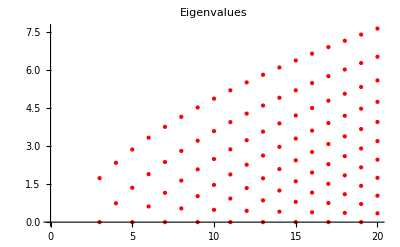

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]
```

## Check Boundary Stability

### Stability Check

```mathematica
CheckBoundary[n_]:=Module[{entropy,error,numEntries,OnsagerMat},

OnsagerMat =MatOnsager[n];
error =Simplify[ OnsagerMat-Transpose[OnsagerMat]];
numEntries=Length[Flatten[OnsagerMat]];

Print[Style["Num Tensors: ",FontColor->Black],n];
Print[Style["Checking Symmetricity",FontColor->Magenta]];
If[Count[Flatten[error],0]==numEntries,Print[Style["Symmetric",FontColor->Green]],Print[Style["UnSymmetric",FontColor->Red]]];

Print[Style["Checking Eigenvalues",FontColor->Brown]];
(*equality with zero will exists because of no penetration boundary condition*)
If[Length[Select[Eigenvalues[OnsagerMat],#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];

]


CheckSSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

(*check for the symmetricity of the matrices by computing A - Transpose[A]*)
If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

(*compute the positive definetness by computing the eigenvalues*)
If[Length[Select[EV,#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Semi-Definite",FontColor->Green]]];
]
```

```mathematica
Ntensors = Range[4,20,1];
Do[CheckBoundary[ii],{ii,Ntensors}];
```

Num Tensors: 4

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 5

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 6

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 7

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 8

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 9

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 10

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 11

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 12

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 13

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 14

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 15

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 16

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 17

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 18

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 19

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 20

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

## Gauss Hermite Quadrature Routines

```mathematica
(*N is the number of quadrature points needed.*)
GaussHermiteQuadrature[points_]:=Module[{locations,weights},

(*location of the gauss quadrautre points*)
locations =Chop[ N[x/.{ToRules@Roots[H[points,x]==0,x]}]];

(*weights of the gauss quadrature*)
weights = Table[(Coefficient[H[points,c],c^points]Integrate[f0[c] H[points-1,c]^2,{c,-∞,∞}])/(Coefficient[H[points-1,c],c^(points-1)](D[H[points,c],c]/.c->locations⟦ii⟧)(H[points-1,c]/.c->locations⟦ii⟧)),{ii,1,points}];

{locations,weights}

]

GaussHermitePoints = Table[GaussHermiteQuadrature[ii],{ii,2,25}];

(*f is the function which we wish to integrate and N is the number of quadrature points which we want to use in order to integrate*)
PerformNumericalIntegration[f_,M_]:=Module[{points,result},
points = GaussHermitePoints⟦M-1⟧;
result = 0;
Do[result=result+((f )/.{c->points⟦1⟧⟦ii⟧})*points⟦2⟧⟦ii⟧,{ii,1,Length[points⟦1⟧]}];
result
]
```

### Convergence analysis for integration

```mathematica
Clear[Integrand]
Integrand[c_]:=H[4,c]^2;
TrialPoints = 20;
Error=Flatten[ConstantArray[0,{1,TrialPoints-1}]];
TrueValue = Integrate[Integrand[c]f0[c],{c,-∞,∞}];
Do[Error⟦ii-1⟧=Abs[TrueValue-PerformNumericalIntegration[Integrand[c],ii]],{ii,2,TrialPoints}];
```

```mathematica
TrueValue
```

1

```mathematica
Error
```

{0.833333,0.25,1.,0.,2.06347×10^-15,6.72911×10^-16,2.55352×10^-15,6.66134×10^-16,3.77476×10^-15,6.21725×10^-15,9.10383×10^-15,7.54952×10^-15,4.44089×10^-16,2.64233×10^-14,1.42997×10^-13,4.77396×10^-14,1.46549×10^-14,4.39648×10^-14,2.68008×10^-13}

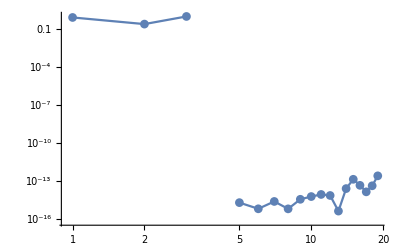

```mathematica
ListLogLogPlot[Error,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

## Boundary Conditions Quadrature points

```mathematica
BoundaryQuadPoints[Ntensors_]:=Module[{fW,locations,fGas,IDOdd,IDEven,OddVar,EvenVar,BC,g,Boe,WallDistribution,VelocityWall,f,BoundaryMoments,EntropyFlux,GaussPoints},

IDOdd = If[EvenQ[Ntensors],Range[1,Ntensors-1,2],Range[1,Ntensors-2,2]];
IDEven = If[EvenQ[Ntensors],Range[0,Ntensors-2,2],Range[0,Ntensors-1,2]];
GaussPoints=24;


(*distribution function at the wall. Without f0*)
fW[c_]:=Piecewise[{{( rhoW H[0,c]+αW[2] H[2,c]),c<0},{fG[c,Ntensors]/f0[c],c≥0}}];

(*determination of the density at the wall. Velocity at the wall*)
VelocityWall=PerformNumericalIntegration[fW[c]c,GaussPoints];

(*The condition on a zero wall velocity now provides us with an expression for the density of the wall*)
f[c]=fW[c]/.Solve[VelocityWall==0,rhoW]⟦1⟧;


(*compute the tensors on the boundary*)
BoundaryMoments=Chop[Simplify[Table[PerformNumericalIntegration[f[c]H[ii,c],GaussPoints]-α[ii]==0,{ii,IDOdd}]]];


BoundaryMoments=(Map[α[#]&,IDOdd]/.Solve[BoundaryMoments,Map[α[#]&,IDOdd]]⟦1⟧)/.{α[1]->0};


(*we now collect the matrix Boe*)
{g,Boe}=N[CoefficientArrays[BoundaryMoments,Map[α[#]&,IDEven]]];

(*EntropyFlux=Transpose[Boe].MatAoe[Ntensors];
CheckSSPD[EntropyFlux,"EntropyFlux"];
*)
Boe

]
```

#### Checking Boundary Conditions

```mathematica
Do[BoundaryQuadPoints[ii],{ii,Range[5,13]}];
```

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

EntropyFlux

Symmetric

Positive Semi-Definite

## Construct Boundary Conditions

### core routine

```mathematica
(*flag == 0 for MBCs,flag == 1 for OBCs*)
ConstructStableBC[n_,flag_]:=Module[{BCMat,OddVar,EvenVar,IDEven,IDOdd,result,Boe},


IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=Flatten[ConstantArray[0,{Length[IDOdd]-1}]];

OddVar=Map[α[#]&,IDOdd];
EvenVar=Map[α[#]&,IDEven];

Which[flag==0,Boe=MatBoe[n];,flag==1,Boe=MatOnsager[n].MatAoe[n];,flag==2,Boe=BoundaryQuadPoints[n]];

(*we neglect the first boundary condition*)
Do[result⟦ii⟧=α[IDOdd⟦ii+1⟧]-Boe⟦ii+1,All⟧.Map[α[#]&,IDEven]+Boe⟦ii+1,2⟧/(√2)θW,{ii,1,Length[IDOdd]-1}];

Expand[Simplify[result]]
]
```

```mathematica
(*Do[bc0[ii]=ConstructStableBC[ii,0];
bc0Stable[ii]=ConstructStableBC[ii,1];,{ii,5,50}];*)
```

```mathematica
AA[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

```mathematica
Clear[bc]
```

### OnsagerMatrices

```mathematica
min=4;
max=20;
```

```mathematica
(*The original onsager coefficients*)
Do[onsagerOld[ii]=MatOnsager[ii],{ii,min,max}];
```

```mathematica
(*onsager matrices which have positivity and symmetricity*)
(*Do[{onsagercoeff[ii],onsagerNew[ii]}=FixOnsager[onsagerOld[ii]]⟦{1,-1}⟧,{ii,min,max}];*)
```

### Boundary Conditions

```mathematica
Do[bcMBC[ii]=ConstructStableBC[ii,0],{ii,min,max}];

Do[bcPBC[ii]=ConstructStableBC[ii,1],{ii,min,max}];
```

## Solving Routines

### returns the solution

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolution[nvar_,kn_,thetaw_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (*heat flux constant*)

(*the following ansatz is the particular solution to the problem. The problem is linear therefore it is enough to consider upto first order polynomials as the ansatz. Such ansatz is only possible because of a bounded domain. On an unbounded domain, we cannot do this.*)

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

(*The following additon of the eigenmodes is the homogeneous solution to the problem. But why the term C0B0?*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}
(*{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn}*)
]
```

### returns the distribution function

```mathematica
(*flag = 0 for unstable, flag == 1 for stable*)
Getf[nvar_,kn_,thetaw_,flag_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc0,result},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


If[flag==0,bc0=ConstructStableBC[nvar,0],bc0=ConstructStableBC[nvar,1]];

bcEqn=Table[bc0⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)

res/.solBC/.{Kn->kn}
]
```

### returns the error

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetErrorEstimate[nvar_,kn_,thetaw_,bcinput_,B0_]:=Block[{λ0,λ,λPlus,v,vv,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]-B0,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)
{{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn},res,solBC}
]
```

## Acceleration

### Accelerate series expansion

```mathematica
(*gives the output of accelerated series*)
CreateAcc[list_]:=Module[{size,Sn,result},
size = Length[list];

(*binomial series corresponding to each term*)
Sn = ConstantArray[0,size];
Do[Sn⟦ii⟧=Sum[(-1)^(jj-1)Binomial[ii-1,jj-1]list⟦ii-jj+1⟧,{jj,1,ii}],{ii,1,size}];

result = Sum[(-1)^(ii-1)Sn⟦ii⟧/2^ii,{ii,1,size}]
]
```

#### coeffs of a_k

```mathematica
(*in the following routine we compute the coefficients of Subscript[a, k]
N = total terms-1, r = k*)
Coeffak[N_,r_]:=(-1)^r Sum[Binomial[N-j,N-r-j]/2^(N-j+1),{j,0,N-r}];
```

#### Averaging factor

```mathematica
(*the following is the factor which should be used while averagin the final result of the accelerated series*)
CoeffAvg[N_]:=Sum[Abs[Coeffak[N,r]],{r,0,N}];
```

### Accelerated solution

```mathematica
AccSolution[list_]:=Module[{ak,AccSol},
ak = Table[(-1)^(ii-1)list⟦ii⟧,{ii,1,Length[list]}];
AccSol = CreateAcc[ak]/CoeffAvg[Length[list]-1];
AccSol
]
```

## Discrete Velocity Solution

```mathematica
Arrayθ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧(gaussloc⟦ii⟧^2-1),{ii,1,Length[gaussW]}];
```

### Kn 0.1

```mathematica
exactfKn0p1=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn0p1/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn0p1=exactfKn0p1⟦1,IDpointsc⟧;
pointsxKn0p1=exactfKn0p1⟦1,IDpointsx⟧;
θKn0p1=Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,3⟧].exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,4⟧},{ii,1,pointsxKn0p1}],InterpolationOrder->3];

fKn0p1=Table[Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn0p1}],InterpolationOrder->3],{ii,1,pointsxKn0p1}];
```

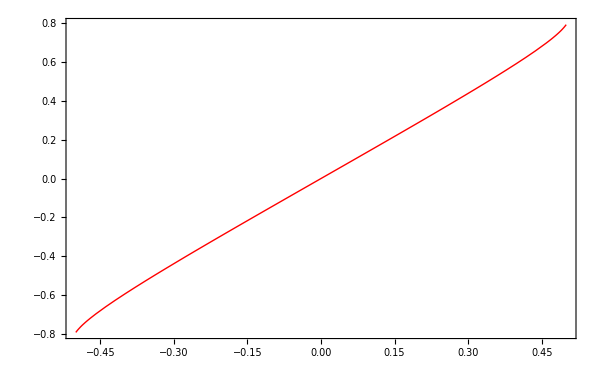

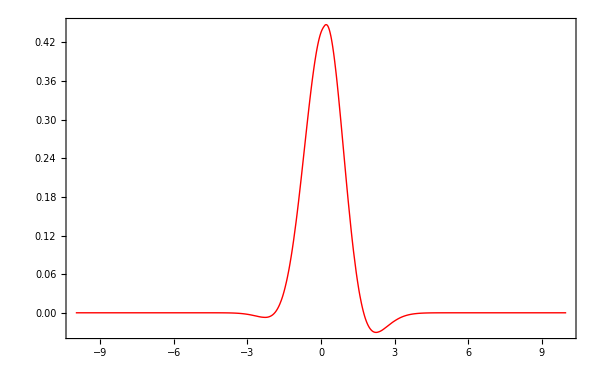

```mathematica
Plot[{θKn0p1[x]},{x,-0.5,0.5}]
Plot[{fKn0p1⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 1.0

```mathematica
exactfKn1p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn1p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn1p0=exactfKn1p0⟦1,IDpointsc⟧;
pointsxKn1p0=exactfKn1p0⟦1,IDpointsx⟧;
θKn1p0=Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,3⟧].exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,4⟧},{ii,1,pointsxKn1p0}],InterpolationOrder->3];

fKn1p0=Table[Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn1p0}],InterpolationOrder->3],{ii,1,pointsxKn1p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

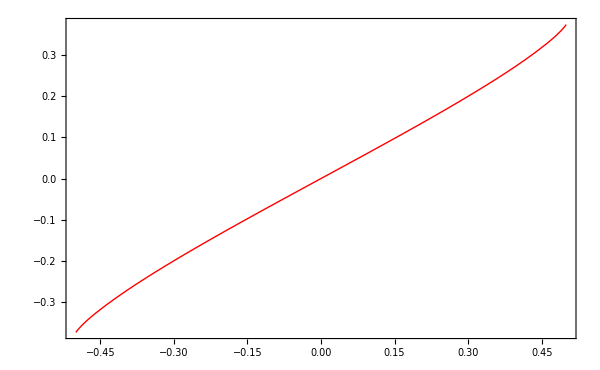

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

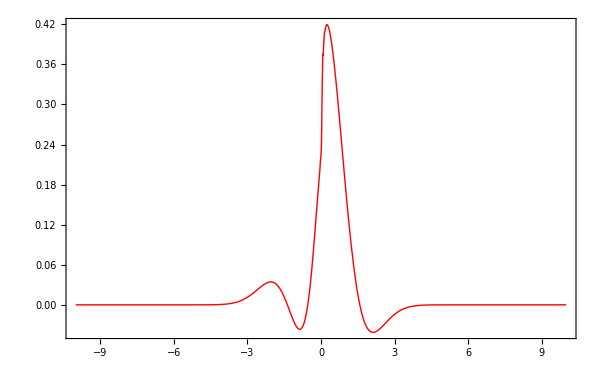

```mathematica
Plot[{θKn1p0[x]},{x,-0.5,0.5}]
Plot[{fKn1p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 10.0

```mathematica
exactfKn10p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn10p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn10p0=exactfKn10p0⟦1,IDpointsc⟧;
pointsxKn10p0=exactfKn10p0⟦1,IDpointsx⟧;
θKn10p0=Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,3⟧].exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,4⟧},{ii,1,pointsxKn10p0}],InterpolationOrder->3];

fKn10p0=Table[Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn10p0}],InterpolationOrder->3],{ii,1,pointsxKn10p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

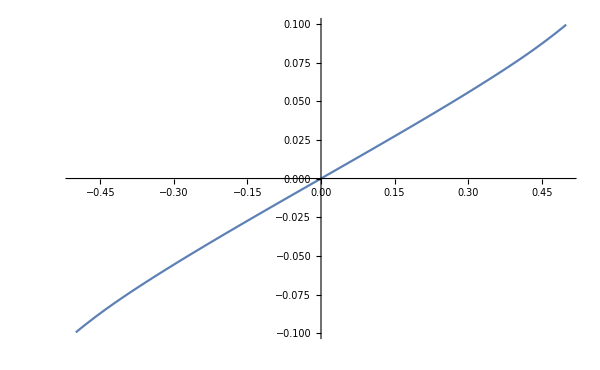

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

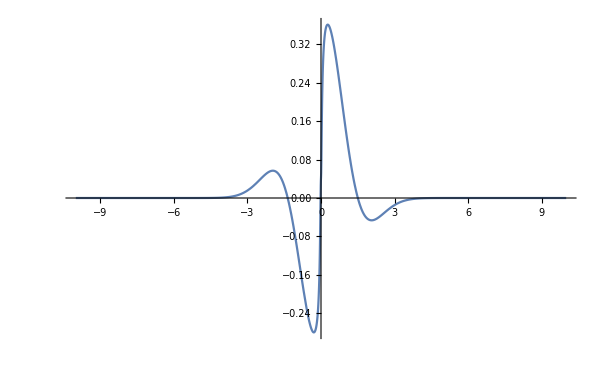

```mathematica
Plot[{θKn10p0[x]},{x,-0.5,0.5}]
Plot[{fKn10p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 100.0

```mathematica
exactfKn100p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kn100p0/fx199c80.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn100p0=exactfKn100p0⟦1,IDpointsc⟧;
pointsxKn100p0=exactfKn100p0⟦1,IDpointsx⟧;
θKn100p0=Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,3⟧].exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,4⟧},{ii,1,pointsxKn100p0}],InterpolationOrder->3];

fKn100p0=Table[Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn100p0}],InterpolationOrder->3],{ii,1,pointsxKn100p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

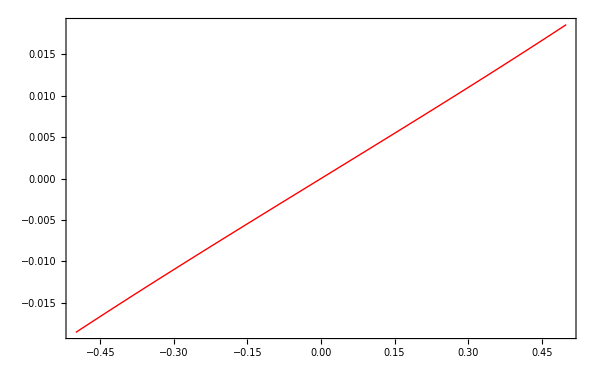

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

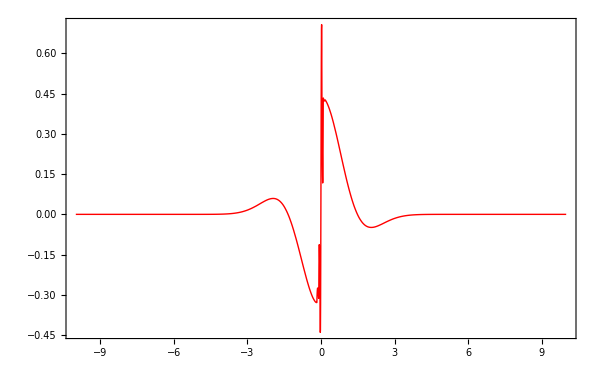

```mathematica
Plot[{θKn100p0[x]},{x,-0.5,0.5}]
Plot[{fKn100p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn ∞

```mathematica
exactfKn∞=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results/Results_Discrete_Velocity/1D_Heat_Conduction/Kninf/fx9c160.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn∞=exactfKn∞⟦1,IDpointsc⟧;
pointsxKn∞=exactfKn∞⟦1,IDpointsx⟧;
θKn∞=Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,3⟧].exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,4⟧},{ii,1,pointsxKn∞}],InterpolationOrder->3];

fKn∞=Table[Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn∞}],InterpolationOrder->3],{ii,1,pointsxKn∞}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

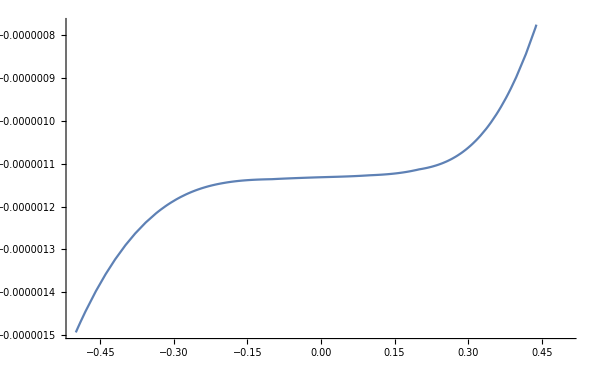

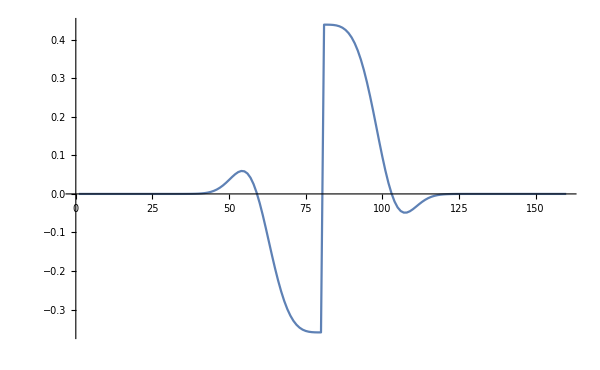

```mathematica
Plot[{Chop[θKn∞[x],10^-7]},{x,-0.5,0.5}]
ListPlot[exactfKn∞⟦IDdata+1;;IDdata+pointscKn∞,4⟧,PlotRange->Full,Joined->True]
```

## High Order Moment (Reference)

```mathematica
VarRef = 20;
```

```mathematica
bcRef=ConstructStableBC[VarRef,1];
```

```mathematica
bcRef
```

{(2 θW)/(√(3 π))-2 √(2/(3 π)) α[2]+α[3]-2/3 √(2/π) α[4]+α[6]/(√(15 π))-√(2/(105 π)) α[8]+(5 α[10])/(12 √(21 π))-1/12 √(7/(11 π)) α[12]+(7 α[14])/(8 √(286 π))-1/4 √(11/(390 π)) α[16]+1/64 √(429/(85 π)) α[18],-(2 θW)/(√(15 π))+2 √(2/(15 π)) α[2]-2 √(2/(5 π)) α[4]+α[5]-3/5 √(3/π) α[6]+√(2/(21 π)) α[8]-1/4 √(7/(15 π)) α[10]+(9 α[12])/(4 √(385 π))-7/24 √(11/(130 π)) α[14]+1/20 √(39/(22 π)) α[16]-9/64 √(33/(221 π)) α[18],(3 θW)/(√(70 π))-(3 α[2])/(√(35 π))+√(5/(21 π)) α[4]-(9 α[6])/(2 √(14 π))+α[7]-(15 α[8])/(14 √π)+5/24 √(5/(2 π)) α[10]-9/8 √(3/(110 π)) α[12]+3/32 √(165/(91 π)) α[14]-1/48 √(143/(7 π)) α[16]+135/128 √(13/(2618 π)) α[18],-1/3 √(5/(7 π)) θW+1/3 √(10/(7 π)) α[2]-1/3 √(14/(15 π)) α[4]+1/6 √(7/π) α[6]-(5 α[8])/(3 √(2 π))+α[9]-35/72 √(5/π) α[10]+7/8 √(5/(33 π)) α[12]-7/16 √(77/(390 π)) α[14]+1/24 √(143/(14 π)) α[16]-5/384 √(1001/(17 π)) α[18],5/12 √(7/(22 π)) θW-5/12 √(7/(11 π)) α[2]+5/4 √(3/(77 π)) α[4]-9/8 √(7/(110 π)) α[6]+5/8 √(5/(11 π)) α[8]-(175 α[10])/(32 √(22 π))+α[11]-315/352 √(3/(2 π)) α[12]+35/128 √(21/(13 π)) α[14]-3/64 √(91/(5 π)) α[16]+135/512 √(65/(238 π)) α[18],-3/4 √(21/(286 π)) θW+3/4 √(21/(143 π)) α[2]-1/12 √(77/(13 π)) α[4]+9/8 √(33/(910 π)) α[6]-3/8 √(33/(65 π)) α[8]+35/32 √(11/(78 π)) α[10]-(189 α[12])/(32 √(26 π))+α[13]-(693 √(7/π) α[14])/1664+11/64 √(21/(5 π)) α[16]-297/512 √(21/(170 π)) α[18],7/16 √(11/(65 π)) θW-7/8 √(11/(130 π)) α[2]+7/8 √(13/(330 π)) α[4]-7/480 √(143/π) α[6]+1/16 √(143/(14 π)) α[8]-7/384 √(1001/(5 π)) α[10]+7/128 √(273/(5 π)) α[12]-539/256 √(3/(10 π)) α[14]+α[15]-(1001 α[16])/(640 √(2 π))+(3003 α[18])/(2048 √(17 π)),-1/8 √(143/(85 π)) θW+1/4 √(143/(170 π)) α[2]-1/4 √(165/(442 π)) α[4]+9/16 √(13/(187 π)) α[6]-5/24 √(143/(238 π)) α[8]+5/64 √(715/(119 π)) α[10]-9/64 √(273/(85 π)) α[12]+77/128 √(15/(34 π)) α[14]-(429 α[16])/(64 √(34 π))+α[17]-(19305 α[18])/(17408 √π),9/64 √(715/(646 π)) θW-9/64 √(715/(323 π)) α[2]+1/64 √(7293/(95 π)) α[4]-27/128 √(187/(494 π)) α[6]+45/128 √(221/(1463 π)) α[8]-(5 √(85085/(38 π)) α[10])/1536+27/512 √(3315/(266 π)) α[12]-(693 √(51/(95 π)) α[14])/2048+(429 √(17/(19 π)) α[16])/1024-(57915 α[18])/(8192 √(38 π))+α[19]}

### Kn 0.1

```mathematica
HighOrderKn0p1[x_] = GetSolution[VarRef,0.1,1.0,bcRef]⟦1,1⟧;
```

### Kn 1.0

```mathematica
HighOrderKn1p0[x_] = GetSolution[VarRef,1.0,1.0,bcRef]⟦1,1⟧;
```

### Kn 10.0

```mathematica
HighOrderKn10p0[x_] = GetSolution[VarRef,10.0,1.0,bcRef]⟦1,1⟧;
```

### Kn 100.0

```mathematica
HighOrderKn100p0[x_] = GetSolution[VarRef,100.0,1.0,bcRef]⟦1,1⟧;
```

## Return Error

```mathematica
(*Returns the error. Flag == 0 for MBC, Flag == 1 for PBC and Flag == 2 for PBCOptimal*)
ReturnError[nvar_,Kn_,flag_,ref_]:=Module[{onsagerMat,bc,solution,error,time1,time2,gaussx,gaussW,domain},

If[nvar <min || nvar >max,Print[Style["Variables beyond present theory",FontColor->Red]]];

Which[flag==0,
bc=bcMBC[nvar];,
flag==1,
bc=bcPBC[nvar];,
flag==2,
bc=bcPBCQuadPoints[nvar];];


time1=AbsoluteTiming[
solution[x_]=GetSolution[nvar,Kn,1.0,bc]⟦1,1⟧;];

error = NIntegrate[Abs[solution[x]-ref[x]],{x,-0.5,0.5}];

error

]

(*returns the error corresponding to averaged solution *)
ReturnErrorAvg[min_,max_,Kn_,ref_]:=Module[{solution,solutionAvg,bc,gaussW,gaussx,error},

(*loop over all the possible nvars *)
Do[bc= bcPBC[ii];
solution[ii][x_]=GetSolution[ii,Kn,1.0,1,bc]⟦1,1⟧;,{ii,min,max}];

Print[Style["Obtained solution",FontColor->Cyan]];

Do[solutionAvg[ii][x_]=Mean[Table[solution[jj][x],{jj,min,ii}]],{ii,min,max}];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;


Which[Kn==0.1,
Print[Style["Computing error for Kn = 0.1",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==1.0,
Print[Style["Computing error for Kn = 1.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==10.0,
Print[Style["Computing error for Kn = 10.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==100.0,
Print[Style["Computing error for Kn = 100.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];
];

error
]

(*Error from accelerated series expansion*)
ReturnErrorAcc[min_,max_,Kn_,ref_]:=Module[{solution,solutionAvg,bc,gaussW,gaussx,error},

(*loop over all the possible nvars *)
Do[bc= bcPBC[ii];
solution[ii][x_]=GetSolution[ii,Kn,1.0,1,bc]⟦1,1⟧;,{ii,min,max}];

Print[Style["Obtained solution",FontColor->Cyan]];

Do[solutionAvg[ii][x_]=AccSolution[Table[solution[jj][x],{jj,min,ii}]],{ii,min,max}];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;


Which[Kn==0.1,
Print[Style["Computing error for Kn = 0.1",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==1.0,
Print[Style["Computing error for Kn = 1.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==10.0,
Print[Style["Computing error for Kn = 10.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];,
Kn==100.0,
Print[Style["Computing error for Kn = 100.0",FontColor->Green]];
error=Table[Sum[gaussW⟦jj⟧Abs[(solutionAvg[ii][x]/.{x->gaussx⟦jj⟧})-ref[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,min,max}];
];

error
]
```

## Results

### Writting routine

```mathematica
WriteError[result_,filename_,Ntensors_]:=Module[{str},

str=OpenWrite[StringJoin[WriteDirectory,"/",filename,ToString[Ntensors],".dat"]];

(*Write the number of tensors and the optimal error value*)
WriteString[str," Tensors ",ToString[Ntensors]," Optimal Error ",result⟦2⟧,"\n"];
WriteString[str," #error","\n"];

Do[WriteString[str,ToString[result⟦3⟧⟦ii⟧],"\n"];,{ii,1,Length[result⟦3⟧]}];

Close[str];
]
```

### MBC

#### Kn = 0.1

```mathematica
Do[resultMBCKn0p1[ii]=ReturnError[ii,0.1,0,θKn0p1],{ii,min,max}];
```

#### Kn = 1.0

```mathematica
Do[resultMBCKn1p0[ii]=ReturnError[ii,1,0,HighOrderKn1p0],{ii,min,max}];
```

#### Kn = 10.0

```mathematica
Do[resultMBCKn10p0[ii]=ReturnError[ii,10.0,0,HighOrderKn10p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00647,Null}

Time in error computation {0.00248,Null}

Time in solving {0.00663,Null}

Time in error computation {0.00211,Null}

Time in solving {0.01063,Null}

Time in error computation {0.0017,Null}

Time in solving {0.0147,Null}

Time in error computation {0.00283,Null}

Time in solving {0.01742,Null}

Time in error computation {0.00176,Null}

Time in solving {0.01917,Null}

Time in error computation {0.00173,Null}

Time in solving {0.02659,Null}

Time in error computation {0.00183,Null}

Time in solving {0.03031,Null}

Time in error computation {0.00199,Null}

Time in solving {0.03997,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04295,Null}

Time in error computation {0.00216,Null}

Time in solving {0.05869,Null}

Time in error computation {0.0021,Null}

Time in solving {0.06734,Null}

Time in error computation {0.00277,Null}

Time in solving {0.08951,Null}

Time in error computation {0.00213,Null}

Time in solving {0.10147,Null}

Time in error computation {0.00364,Null}

Time in solving {0.12668,Null}

Time in error computation {0.00233,Null}

#### Kn = 100.0

```mathematica
Do[resultMBCKn100p0[ii]=ReturnError[ii,100.0,0,HighOrderKn100p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00577,Null}

Time in error computation {0.00179,Null}

Time in solving {0.00685,Null}

Time in error computation {0.00169,Null}

Time in solving {0.01151,Null}

Time in error computation {0.00162,Null}

Time in solving {0.01211,Null}

Time in error computation {0.00166,Null}

Time in solving {0.01664,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01918,Null}

Time in error computation {0.00171,Null}

Time in solving {0.02516,Null}

Time in error computation {0.00181,Null}

Time in solving {0.0304,Null}

Time in error computation {0.0018,Null}

Time in solving {0.0378,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04597,Null}

Time in error computation {0.00221,Null}

Time in solving {0.06265,Null}

Time in error computation {0.00405,Null}

Time in solving {0.09452,Null}

Time in error computation {0.00224,Null}

Time in solving {0.0877,Null}

Time in error computation {0.00229,Null}

Time in solving {0.10373,Null}

Time in error computation {0.00253,Null}

Time in solving {0.10931,Null}

Time in error computation {0.00212,Null}

### PBC

#### Kn = 0.1

```mathematica
Do[resultPBCKn0p1[ii]=ReturnError[ii,0.1,1,θKn0p1],{ii,min,max}];
```

#### Kn = 1.0

```mathematica
Do[resultPBCKn1p0[ii]=ReturnError[ii,1,1,HighOrderKn1p0],{ii,min,max}];
```

#### Kn = 10.0

```mathematica
Do[resultPBCKn10p0[ii]=ReturnError[ii,10.0,1,HighOrderKn10p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00711,Null}

Time in error computation {0.00182,Null}

Time in solving {0.00649,Null}

Time in error computation {0.00156,Null}

Time in solving {0.01094,Null}

Time in error computation {0.00187,Null}

Time in solving {0.01106,Null}

Time in error computation {0.00174,Null}

Time in solving {0.01573,Null}

Time in error computation {0.00189,Null}

Time in solving {0.02021,Null}

Time in error computation {0.00183,Null}

Time in solving {0.02627,Null}

Time in error computation {0.00191,Null}

Time in solving {0.02955,Null}

Time in error computation {0.00181,Null}

Time in solving {0.03855,Null}

Time in error computation {0.00195,Null}

Time in solving {0.04599,Null}

Time in error computation {0.00211,Null}

Time in solving {0.06044,Null}

Time in error computation {0.00207,Null}

Time in solving {0.07012,Null}

Time in error computation {0.00206,Null}

Time in solving {0.08705,Null}

Time in error computation {0.00282,Null}

Time in solving {0.097547,Null}

Time in error computation {0.00231,Null}

Time in solving {0.10751,Null}

Time in error computation {0.00209,Null}

#### Kn = 100.0

```mathematica
Do[resultPBCKn100p0[ii]=ReturnError[ii,100.0,1,HighOrderKn100p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00632,Null}

Time in error computation {0.00166,Null}

Time in solving {0.0103,Null}

Time in error computation {0.00157,Null}

Time in solving {0.01186,Null}

Time in error computation {0.00226,Null}

Time in solving {0.01225,Null}

Time in error computation {0.00166,Null}

Time in solving {0.01735,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01946,Null}

Time in error computation {0.0017,Null}

Time in solving {0.02542,Null}

Time in error computation {0.0018,Null}

Time in solving {0.03071,Null}

Time in error computation {0.00177,Null}

Time in solving {0.03953,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04555,Null}

Time in error computation {0.00208,Null}

Time in solving {0.06034,Null}

Time in error computation {0.00215,Null}

Time in solving {0.07308,Null}

Time in error computation {0.00292,Null}

Time in solving {0.08558,Null}

Time in error computation {0.00257,Null}

Time in solving {0.11085,Null}

Time in error computation {0.00215,Null}

Time in solving {0.11369,Null}

Time in error computation {0.00252,Null}

### PBC Quadrature points

#### Kn = 0.1

```mathematica
Do[resultPBCQuadPointsKn0p1[ii]=ReturnError[ii,0.1,2,HighOrderKn0p1],{ii,min,max}];
```

#### Kn = 1.0

```mathematica
Do[resultPBCQuadPointsKn1p0[ii]=ReturnError[ii,1,2,HighOrderKn1p0],{ii,min,max}];
```

#### Kn = 10.0

```mathematica
Do[resultPBCKn10p0[ii]=ReturnError[ii,10.0,1,HighOrderKn10p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00711,Null}

Time in error computation {0.00182,Null}

Time in solving {0.00649,Null}

Time in error computation {0.00156,Null}

Time in solving {0.01094,Null}

Time in error computation {0.00187,Null}

Time in solving {0.01106,Null}

Time in error computation {0.00174,Null}

Time in solving {0.01573,Null}

Time in error computation {0.00189,Null}

Time in solving {0.02021,Null}

Time in error computation {0.00183,Null}

Time in solving {0.02627,Null}

Time in error computation {0.00191,Null}

Time in solving {0.02955,Null}

Time in error computation {0.00181,Null}

Time in solving {0.03855,Null}

Time in error computation {0.00195,Null}

Time in solving {0.04599,Null}

Time in error computation {0.00211,Null}

Time in solving {0.06044,Null}

Time in error computation {0.00207,Null}

Time in solving {0.07012,Null}

Time in error computation {0.00206,Null}

Time in solving {0.08705,Null}

Time in error computation {0.00282,Null}

Time in solving {0.097547,Null}

Time in error computation {0.00231,Null}

Time in solving {0.10751,Null}

Time in error computation {0.00209,Null}

#### Kn = 100.0

```mathematica
Do[resultPBCKn100p0[ii]=ReturnError[ii,100.0,1,HighOrderKn100p0]⟦-2⟧,{ii,min,max}];
```

Time in solving {0.00632,Null}

Time in error computation {0.00166,Null}

Time in solving {0.0103,Null}

Time in error computation {0.00157,Null}

Time in solving {0.01186,Null}

Time in error computation {0.00226,Null}

Time in solving {0.01225,Null}

Time in error computation {0.00166,Null}

Time in solving {0.01735,Null}

Time in error computation {0.00171,Null}

Time in solving {0.01946,Null}

Time in error computation {0.0017,Null}

Time in solving {0.02542,Null}

Time in error computation {0.0018,Null}

Time in solving {0.03071,Null}

Time in error computation {0.00177,Null}

Time in solving {0.03953,Null}

Time in error computation {0.00187,Null}

Time in solving {0.04555,Null}

Time in error computation {0.00208,Null}

Time in solving {0.06034,Null}

Time in error computation {0.00215,Null}

Time in solving {0.07308,Null}

Time in error computation {0.00292,Null}

Time in solving {0.08558,Null}

Time in error computation {0.00257,Null}

Time in solving {0.11085,Null}

Time in error computation {0.00215,Null}

Time in solving {0.11369,Null}

Time in error computation {0.00252,Null}

### Plots

#### Kn = 0.1

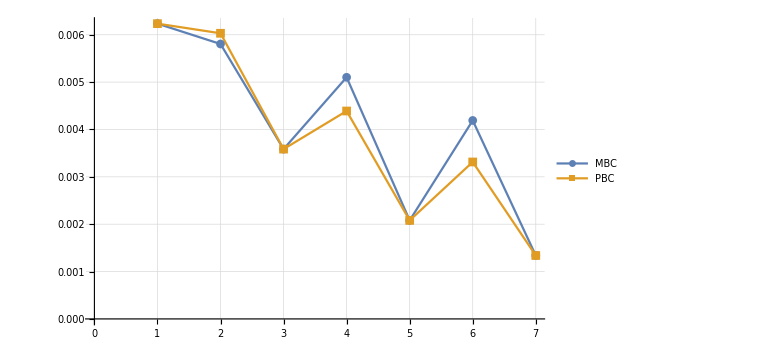

```mathematica
ListPlot[{Table[resultMBCKn0p1[ii],{ii,min,max}],Table[resultPBCKn0p1[ii],{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCQuadPoints"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 1.0

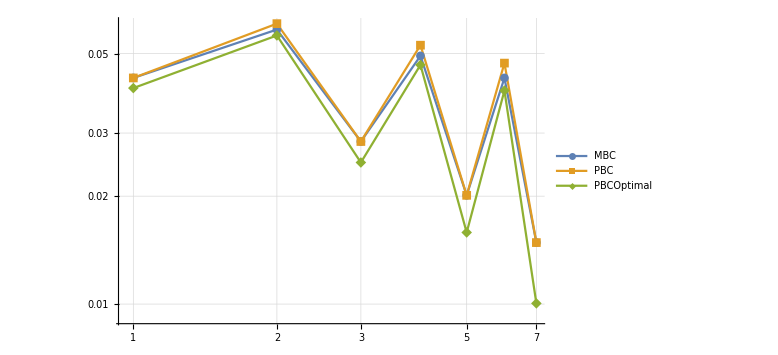

```mathematica
ListLogLogPlot[{Table[resultMBCKn1p0[ii],{ii,min,max}],Table[resultPBCKn1p0[ii],{ii,min,max}],Table[resultPBCQuadPointsKn1p0[ii],{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 10.0

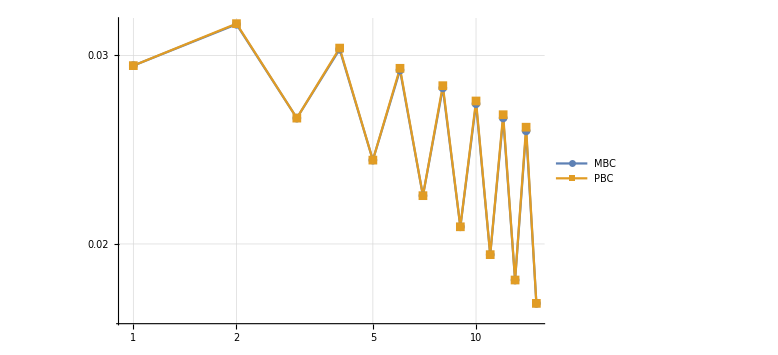

```mathematica
ListLogLogPlot[{Table[resultMBCKn10p0[ii][x],{ii,min,max}],Table[resultPBCKn10p0[ii][x],{ii,min,max}](*,Table[resultPBCOptKn10p0[ii][x]⟦2⟧,{ii,min,max}]*)},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

### Plots for paper

#### plotting routine

```mathematica
PlotError[error_,Kn_]:=Module[{numvariations,ptlegends,TicksXAxis,legendfont},

(*Number of variations which we allow in the plot*)
numvariations=Length[error];
If[numvariations==1,Print[Style["Not Implemeneted",FontColor->Red]]];

legendfont = 16;
Which[numvariations==2,
ptlegends={Style["MBC",FontSize->legendfont],Style["WPBC",FontSize->legendfont]},
numvariations==3,
ptlegends={Style["MBC",FontSize->legendfont],Style["WPBC",FontSize->legendfont],Style["WPBC-Optimal",FontSize->legendfont]}];

TicksXAxis = Table[{ii-min+1,ii},{ii,min,max,1}];

ListPlot[error,Frame->True,GridLines->Automatic,FrameLabel->{{Style["errorθ",FontSize->16],None},{Style["m",FontSize->16],None}},FrameTicks->{{Automatic,None},{TicksXAxis,None}},ImageSize->600,Joined->True,PlotMarkers->{Graphics[{Red,Thick,Circle[]},ImageSize->14],Graphics[{Green,Thick,Circle[]},ImageSize->10]},PlotStyle->{{Red,Thick},{Green,Thick}},PlotLegends->Placed[{ptlegends},{0.8,0.9}],FrameTicksStyle->{{Directive[FontSize->13,Black],None},{Directive[FontSize->13,{Orange,Black}],None}}]

]
```

#### Kn = 0.1

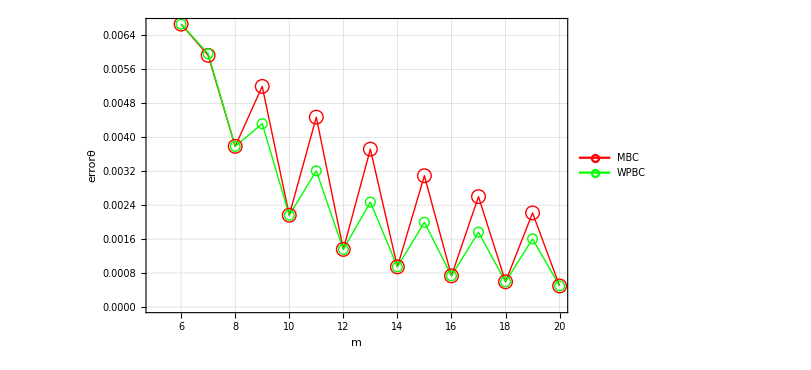

```mathematica
ptKn0p1=PlotError[{Table[resultMBCKn0p1[ii],{ii,min,max}],Table[resultPBCKn0p1[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"Physical_Accuracy/Kn0p1/","error_theta.eps"],ptKn0p1]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn0p1/error_theta.eps

#### Kn = 1.0

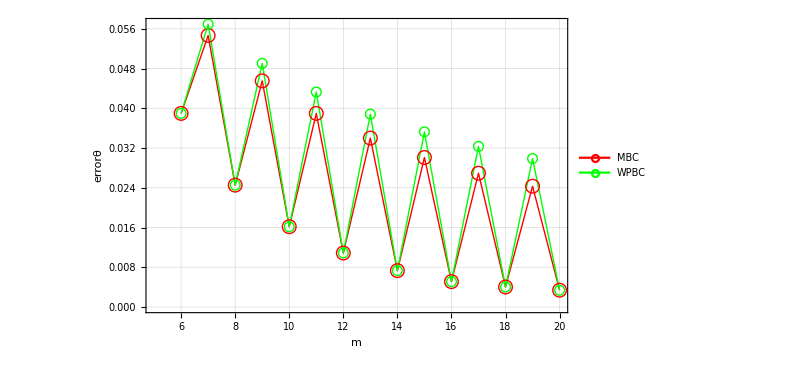

```mathematica
ptKn1p0=PlotError[{Table[resultMBCKn1p0[ii],{ii,min,max}],Table[resultPBCKn1p0[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"/Kn1p0/","error_theta.eps"],ptKn1p0]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn1p0/error_theta.eps

#### Kn = 10.0

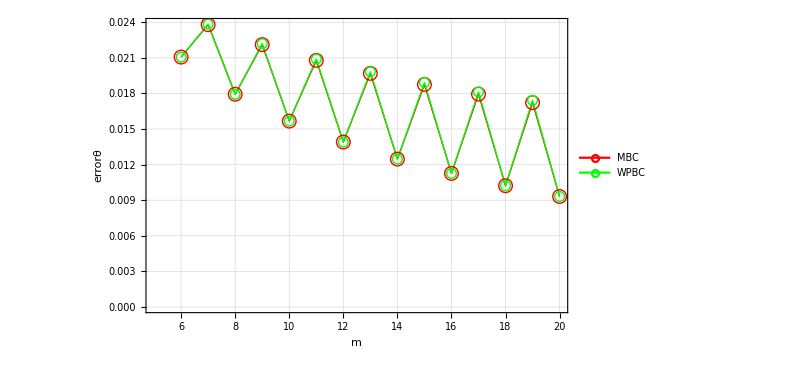

```mathematica
ptKn10p0=PlotError[{Table[resultMBCKn10p0[ii],{ii,min,max}],Table[resultPBCKn10p0[ii],{ii,min,max}]},0.1]
```

```mathematica
Export[StringJoin[WriteDirectoryResults,"/Kn10p0/","error_theta.eps"],ptKn10p0]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Physical_Accuracy/Kn10p0/error_theta.eps

## Results Accelerated

### Kn = 0.1

#### averaged

```mathematica
AvgKn0p1 = ReturnErrorAvg[min,max,0.1,HighOrderKn0p1];
```

Obtained solution

Computing error for Kn = 0.1

{0.00666602,0.00440552,0.00354377,0.0034816,0.00281169,0.00284903,0.00239942,0.0024027,0.0020879,0.00207491,0.00184562,0.0018254,0.00165264,0.00162975,0.00149581}

#### accelerated

```mathematica
AccKn0p1 =  ReturnErrorAcc[min,max,0.1,HighOrderKn0p1]
```

Obtained solution

Computing error for Kn = 0.1

{0.00666602,0.00504433,0.00426377,0.0038767,0.00367544,0.00349083,0.00332148,0.0031659,0.00302271,0.00289068,0.00276871,0.00265583,0.00255114,0.00245387,0.00236333}

### Kn = 1.0

#### averaged

```mathematica
AvgKn1p0 = ReturnErrorAvg[min,max,1.0,HighOrderKn1p0]
```

Obtained solution

Computing error for Kn = 1.0

{0.038961,0.0479452,0.0401386,0.0423638,0.0371229,0.0381469,0.0342488,0.0348195,0.0317637,0.0321126,0.0296356,0.0298597,0.0278034,0.0279508,0.0262128}

#### accelerated

```mathematica
AccKn1p0 =  ReturnErrorAcc[min,max,1.0,HighOrderKn1p0]
```

Obtained solution

Computing error for Kn = 1.0

{0.038961,0.0434531,0.0437475,0.043197,0.0423844,0.0414835,0.0405619,0.0396498,0.0387613,0.0379031,0.037078,0.0362866,0.0355284,0.0348026,0.0341077}

### Kn = 10.0

#### averaged

```mathematica
AvgKn10p0 = ReturnErrorAvg[min,max,10.0,HighOrderKn10p0]
```

Obtained solution

Computing error for Kn = 10.0

{0.0210633,0.0224499,0.0209432,0.0212554,0.0201373,0.0202635,0.0193547,0.0194134,0.0186414,0.0186686,0.0179949,0.0180055,0.0174066,0.0174077,0.016868}

#### accelerated

```mathematica
AccKn10p0 =  ReturnErrorAcc[min,max,10.0,HighOrderKn10p0]
```

Obtained solution

Computing error for Kn = 10.0

{0.0210633,0.0217566,0.0217266,0.0215622,0.0213551,0.0211328,0.0209065,0.0206812,0.0204595,0.0202425,0.0200308,0.0198247,0.0196241,0.0194291,0.0192394}

### Plots

#### plotting routine

```mathematica
PlotErrorAcc[error_,Kn_]:=Module[{numvariations,ptlegends,TicksXAxis,legendfont},

(*Number of variations which we allow in the plot*)
numvariations=Length[error];
If[numvariations==1,Print[Style["Not Implemeneted",FontColor->Red]]];

legendfont = 16;
ptlegends={Style["Averaged Solution",FontSize->legendfont],Style["Euler's Transform",FontSize->legendfont]};

TicksXAxis = Table[{ii-min+1,ii},{ii,min,max,1}];

ListPlot[error,Frame->True,GridLines->Automatic,FrameLabel->{{Style["errorθ",FontSize->16],None},{Style["m",FontSize->16],None}},FrameTicks->{{Automatic,None},{TicksXAxis,None}},ImageSize->600,Joined->True,PlotMarkers->{Graphics[{Red,Thick,Circle[]},ImageSize->14],Graphics[{Green,Thick,Circle[]},ImageSize->10],
Graphics[{Blue,Thick,Circle[]},ImageSize->10]},PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},PlotLegends->Placed[{ptlegends},{0.8,0.9}],FrameTicksStyle->{{Directive[FontSize->13,Black],None},{Directive[FontSize->13,{Orange,Black}],None}}]

]
```

#### Kn = 0.1

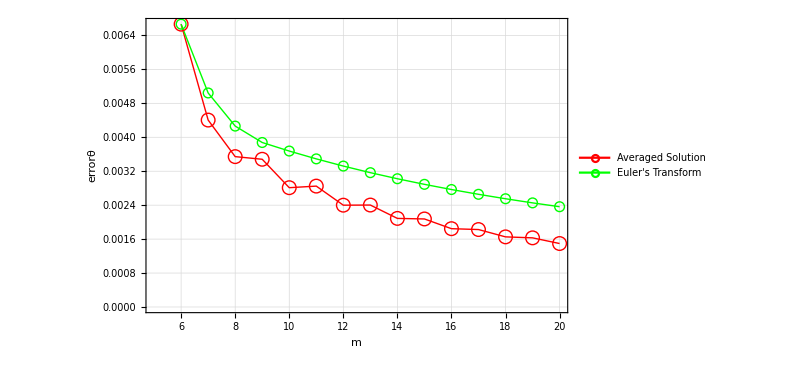

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn0p1/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn0p1,AccKn0p1},0.1]
Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn0p1/","error_theta.eps"],plt]
```

#### Kn = 1.0

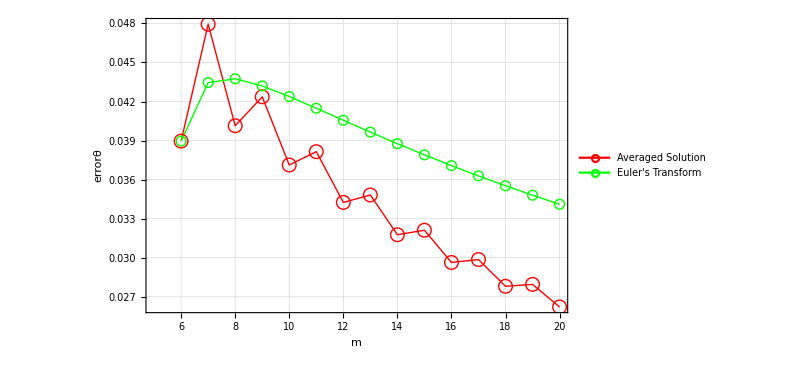

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn1p0/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn1p0,AccKn1p0},0.1]

Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn1p0/","error_theta.eps"],plt]
```

#### Kn = 10.0

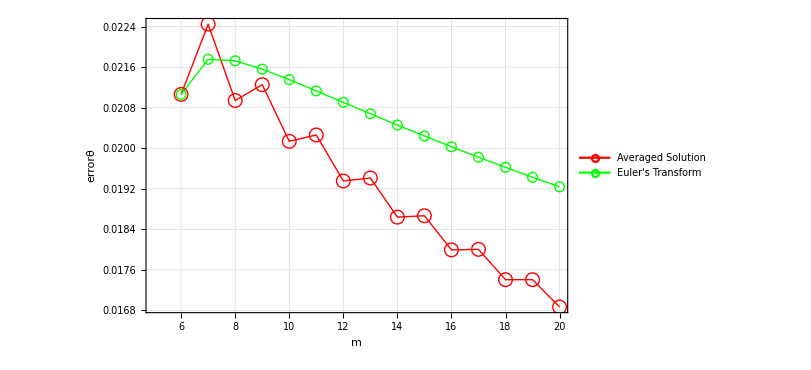

/Users/neerajsarna/Dropbox/my_papers/Publications/1D_Well_Posed_System/Results/Accelerated_Convergence/Kn10p0/error_theta.eps

```mathematica
plt=PlotErrorAcc[{AvgKn10p0,AccKn10p0},10.0]
Export[StringJoin[WriteDirectoryResults,"Accelerated_Convergence/Kn10p0/","error_theta.eps"],plt]
```

## Results for C-code

```mathematica
Kn = 0.1;
```

### G20

```mathematica
(*we only store the value of theta*)
nvar20 = 6;

(*we convert back to basis coefficients*)
sol20 =Chop[Simplify[ (GetSolution[nvar20,Kn,1.0,1,bcPBC[nvar20]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol20]/.{Sinh->sinh}
```

0.9950211932019232*x + 0.009745323921348737*sinh(4.47213595499958*x)

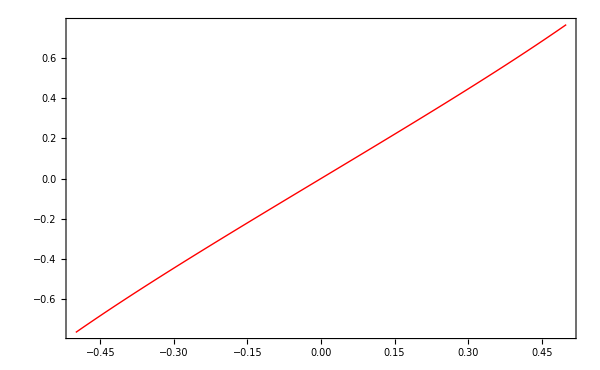

```mathematica
plot2=Plot[sol20 √2,{x,-0.5,0.5}]
```

```mathematica
bcPBC[6]//MatrixForm
```

(0.65147-0.921318 α[2]+α[3]-0.531923 α[4]
-0.291346+0.412026 α[2]-0.71365 α[4]+α[5])

### G26

```mathematica
(*we only store the value of theta*)
nvar26 = 8;

(*we convert back to basis coefficients*)
sol26 =Chop[Simplify[ (GetSolution[nvar26,Kn,1.0,1,bcPBC[nvar26]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol26]/.{Sinh->sinh}
```

0.9918095457622201*x + 0.004077339347408366*sinh(2.517180972479634*x) + 
   0.0031858247584759585*sinh(6.71508535912671*x)

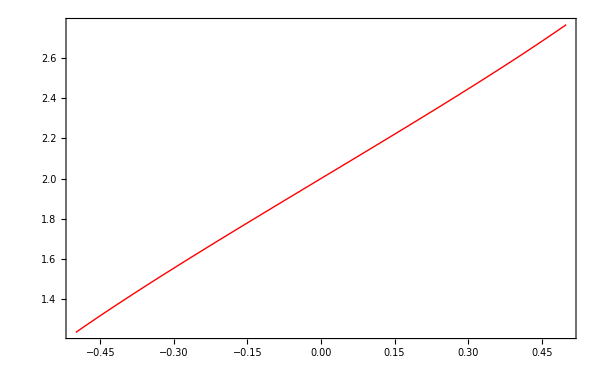

```mathematica
plot2=Plot[sol20+2,{x,-0.5,0.5}]
```

```mathematica
bcPBC[6]//MatrixForm
```

(0.65147-0.921318 α[2]+α[3]-0.531923 α[4]
-0.291346+0.412026 α[2]-0.71365 α[4]+α[5])

### G35

```mathematica
(*we only store the value of theta*)
nvar35 = 9;

(*we convert back to basis coefficients*)
sol35 =Chop[Simplify[ (GetSolution[nvar35,Kn,1.0,1,bcPBC[nvar35]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol35]/.{Sinh->sinh}
```

0.9861871317460368*x + 0.0009740846199919195*sinh(2.2483363346888074*x) + 
   0.008298820931674668*sinh(4.010385905150765*x)

```mathematica
bcPBC[6]//MatrixForm
```

(0.65147-0.921318 α[2]+α[3]-0.531923 α[4]
-0.291346+0.412026 α[2]-0.71365 α[4]+α[5])

### G45

```mathematica
(*we only store the value of theta*)
nvar45 = 11;

(*we convert back to basis coefficients*)
sol45 =Chop[Simplify[ (GetSolution[nvar45,Kn,1.0,1,bcPBC[nvar45]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol45]/.{Sinh->sinh}
```

0.9857643470749898*x + 0.0004959003321893117*sinh(1.9303025585770384*x) + 
   0.002543347245910525*sinh(2.6658847234287704*x) + 0.005290233872198295*sinh(4.9438923511630914*x)

```mathematica
bcPBC[6]//MatrixForm
```

(0.65147-0.921318 α[2]+α[3]-0.531923 α[4]
-0.291346+0.412026 α[2]-0.71365 α[4]+α[5])

### G56

```mathematica
(*the number of tensors in the system*)
nvar56 = 12;

(*we convert back to basis coefficients*)
sol56 =Chop[Simplify[ (GetSolution[nvar56,Kn,1.0,1,bcPBC[nvar56]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol56]/.{Sinh->sinh}
```

0.9899466270992661*x + 0.00010116292970230688*sinh(1.8186266940442457*x) + 
   0.0019797047973874405*sinh(2.3891354429537364*x) + 0.004978603330380985*sinh(3.687003638620778*x) + 
   0.00038639730251888393*sinh(10.604506967165621*x)

### N16

```mathematica
(*the number of tensors in the system*)
nTensors = 16;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol]/.{Sinh->sinh}
```

0.9892927396698521*x + 7.949524702960454e-7*sinh(1.5080981526429016*x) + 
   0.00007599110607032715*sinh(1.8280360908575142*x) + 0.0010765095377805595*sinh(2.2459528687383394*x) + 
   0.003195836632356749*sinh(2.9712749000654357*x) + 0.0032524332462132983*sinh(4.745522597484798*x) + 
   0.0000635644033471918*sinh(13.934429182642614*x)

### N18

```mathematica
(*the number of tensors in the system*)
nTensors = 18;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol]/.{Sinh->sinh}
```

0.9891103738688487*x - 3.4684362295131658e-9*sinh(1.4006653082978795*x) + 
   9.938811076145555e-6*sinh(1.664568126811443*x) + 0.00025689789010162757*sinh(1.9815191312437987*x) + 
   0.001615975388904252*sinh(2.431133592076258*x) + 0.0032265940137877307*sinh(3.2473676118677286*x) + 
   0.002561075578033159*sinh(5.235889289787754*x) + 0.000028099072925427022*sinh(15.450468880651211*x)

### N20

```mathematica
(*the number of tensors in the system*)
nTensors = 20;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];
```

```mathematica
CForm[sol]/.{Sinh->sinh}
```

0.9889757964874321*x + 8.548836749354673e-9*sinh(1.312499845273545*x) + 
   6.425109739508264e-7*sinh(1.5359624765465445*x) + 0.000046769982279263285*sinh(1.7928504374446674*x) + 
   0.0005340677389950208*sinh(2.1202457820361236*x) + 0.002012515257218323*sinh(2.6095498761963127*x) + 
   0.003085495180863663*sinh(3.5141607592624338*x) + 0.0020173922087678656*sinh(5.703742588502402*x) + 
   0.000012998563891241376*sinh(16.88777884716506*x)

### N22

```mathematica
(*the number of tensors in the system*)
nTensors = 22;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];

CForm[sol]/.{Sinh->sinh}
```

0.9888725604237197*x - 1.1267507505527853e-9*sinh(1.238538873534564*x) + 
   1.0425594006751506e-7*sinh(1.4314385108767749*x) + 5.310480436339387e-6*sinh(1.6466429341157962*x) + 
   0.000130574387363048*sinh(1.9067974753769268*x) + 0.0008484475423778083*sinh(2.2508407141902804*x) + 
   0.002257045383117194*sinh(2.7829365376803588*x) + 0.0028667510847416398*sinh(3.771937211055834*x) + 
   0.0015959510715178827*sinh(6.151532393786605*x) + 6.251452487753951e-6*sinh(18.257360408445823*x)

### N24

```mathematica
(*the number of tensors in the system*)
nTensors = 24;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];

CForm[sol]/.{Sinh->sinh}
```

0.9887909148897903*x + 2.1248298302441273e-10*sinh(1.1753915070425638*x) - 
   4.753332814364334e-9*sinh(1.3444672058183817*x) + 7.269127503526152e-7*sinh(1.5286628972393546*x) + 
   0.000021091722168993028*sinh(1.7445093738681328*x) + 0.00026554174814196423*sinh(2.0119506654634387*x) + 
   0.0011453546231374565*sinh(2.376383830762091*x) + 0.0023788884543610805*sinh(2.951828444318971*x) + 
   0.0026215690952677067*sinh(4.0211509594000825*x) + 0.0012699863181260631*sinh(6.581408804336385*x) + 
   3.1095921280567805e-6*sinh(19.56789817463244*x)

### N30

```mathematica
(*the number of tensors in the system*)
nTensors = 30;

(*we convert back to basis coefficients*)
sol =Chop[Simplify[ (GetSolution[nTensors,Kn,1.0,1,bcPBC[nTensors]]⟦1,1⟧)/(√2)]];

CForm[sol]/.{Sinh->sinh}
```

0.9886241450400803*x - 1.4284622829507996e-9*sinh(1.2779468215207301*x) + 
   5.266949286451139e-8*sinh(1.4173548123589153*x) + 1.1902338825856906e-6*sinh(1.5772937256341433*x) + 
   0.00002541376197682671*sinh(1.766211842724685*x) + 0.00020307410067078814*sinh(1.9973620316950804*x) + 
   0.0008206049409972356*sinh(2.29896310304997*x) + 0.0017197261477691537*sinh(2.7338379482754673*x) + 
   0.002324240918088127*sinh(3.4334119104667082*x) + 0.0019292768842024432*sinh(4.722835521599962*x) + 
   0.0006649745620110362*sinh(7.7807719198946925*x) + 4.5110234469975064e-7*sinh(23.209091470407046*x)

## Estimation of error

```mathematica
SolutionM4=GetSolution[20,0.1,1.0,bcPBC[20]];
```

```mathematica
Chop[SolutionM4,10^-6]⟦4⟧//MatrixForm
```

-0.171296

```mathematica
AA[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

```mathematica
AA[4]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)